## CA Manipulation

```mathematica
initialValues=SparseArray[{{1,1}->1,{2,5}->1,{3,10}->1,{1,6}->1},{5,11}]; (* Define starting values and lattice size. *)
```

```mathematica
initialValues//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
cellState[cell_,globalState_]:=globalState[[cell[[1]],cell[[2]]]]; (* Returns the value of the cell {x,y}. *) 
cellState[{1,8},initialValues]
```

0

```mathematica
triangularvNN[cell_,lattice_]:=Module[{c1=cell[[1]],c2=cell[[2]]},
If[EvenQ[c2],
{c1,c2}->{{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2-1}},
{c1,c2}->{{c1-1,c2+1},{c1,c2-1},{c1,c2},{c1,c2+1}}
]
]; (* Gives a rule for associating a cell to its von Neumann neighborhood. *)
```

```mathematica
nbhdTable[lattice_]:=Association[Flatten[Table[triangularvNN[{i,j},lattice],{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}],1]]; (* Associates all cells to their von Neumann neighborhoods. *)
```

```mathematica
vonNeumannNeighborhoods=nbhdTable[initialValues]; (* Evaluate once and use henceforth! *)
```

```mathematica
vonNeumannNeighborhoods[[Key[{1,7}]]]
```

{{0,8},{1,6},{1,7},{1,8}}

```mathematica
neighborhoodState[cell_,globalState_]:=Quiet[Module[{n=vonNeumannNeighborhoods[[Key[cell]]]},
Table[If[IntegerQ[cellState[n[[i]],globalState]],cellState[n[[i]],globalState],0],
{i,1,Length[n]}]
]]; (* Returns the state of each cell in the von Neumann neighborhood of the specified cell. *)
```

```mathematica
rules=<|{0,0}->0,{0,1}->1,{0,2}->1,{0,3}->0,{1,1}->0,{1,2}->1,{1,3}->0,{1,4}->0|>; (* An example set of rules. *)
```

```mathematica
cellEvolution[cell_,globalState_]:=Lookup[rules,{{cellState[cell,globalState],Total[neighborhoodState[cell,globalState]]}}][[1]];
cellEvolution[{1,1},initialValues]
```

0

```mathematica
globalEvolution[state_]:=SparseArray[{i_,j_}->cellEvolution[{i,j},state],Dimensions[state]];
testarray=SparseArray[{i_,j_}->5(i-1)+j,{5,5}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5
6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15
16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25)

```mathematica
evolution[initialValues]
```

Part::pkspec1: The expression i$ cannot be used as a part specification.

SparseArray[…]

## CA Graphics

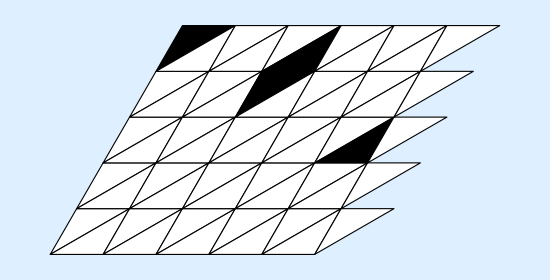
-Graphics-(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{1.5,-(√3)/2},{2.5,-(√3)/2},{1.,-√3}}]}

```mathematica
tLatticePlot[basis_,lattice_]:=Module[{b1=basis[[1]],b2=basis[[2]]},
Table[
If[OddQ[j],
{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],EdgeForm[Black],Triangle[{b1*((j-1)/2)-b2*(i-1),b1*((j+1)/2)-b2*(i-1),b1*(j-1)/2-b2*(i)}]},
{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],EdgeForm[Black],Triangle[{b1*(j/2)-b2*(i-1),b1*(j/2-1)-b2*(i),b1*(j/2)-b2*(i)}]}],
{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}]
];
basis={{1,0},{0.5,Sqrt[3]/2}};
Row[{Graphics[tLatticePlot[basis,initialValues],ImageSize->Dimensions[initialValues][[2]]*50,Background->LightBlue],initialValues//MatrixForm}]
tLatticePlot[basis,initialValues][[2,5]]
```

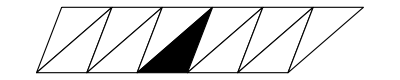

```mathematica
initialValues1D=SparseArray[{1,6}->1,{1,11}];
basis1D={{1,0},{0.5,Sqrt[3]/2}};
Graphics[tLatticePlot[basis1D,initialValues1D]]
```